```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
nnoise=Import["res_bc_ansatz_nnoise.csv"];
```

```mathematica
noise=Import["res_bc_ansatz_noise.csv"];
```

```mathematica
noise[[2;;,2]]
```

{0.57,0.51,0.34,0.35,0.55,0.57,0.65,0.64,0.61,0.3,0.41,0.51,0.6,0.55,0.5,0.68,0.55,0.41,0.7,0.49,0.46,0.57,0.55,0.52,0.46,0.31,0.41}

```mathematica
StandardDeviation[x]
```

0.0615817

```mathematica
x=noise[[2;;,2]];
y=nnoise[[2;;,2]];
```

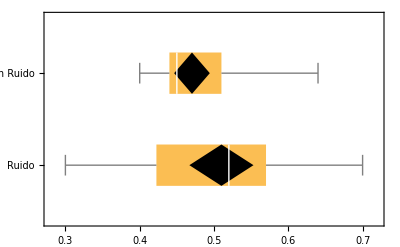

```mathematica
graf=BoxWhiskerChart[{x,y},{"Diamond",{"MeanDiamond",1,Black}},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```

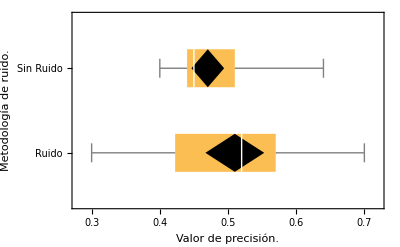

```mathematica
Show[graf,FrameLabel->{{RawBoxes[RowBox[{"Metodología"," ","de"," ",RowBox[{"ruido","."}]}]],None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],HoldForm[Distribución de la ejecución VQC ANSATZ]}},PlotLabel->None,LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export["distributions_credit_ansatz.pdf",%]
```

distributions_credit_ansatz.pdf

```mathematica
With[
{α=0.05,x=noise[[2;;,2]],
y=nnoise[[2;;,2]]},
KolmogorovSmirnovTest[x,y,"TestDataTable", SignificanceLevel->α]]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.37037 | 0.0328981

```mathematica
With[
{α=0.05,x=noise[[2;;,2]],
y=nnoise[[2;;,2]]},
SignedRankTest[{x,y}]]
```

0.0909259

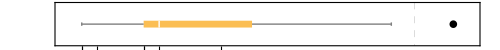

```mathematica
With[{data=nnoise[[2;;,2]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw1=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

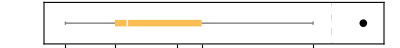

```mathematica
Show[bw1,ImageSize->Full]
```

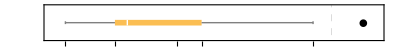

```mathematica
Show[bw1,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Sin ruido)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "distribution_q_ansatz_nnoise_credit.pdf",%]
```

distribution_q_ansatz_nnoise_credit.pdf

```mathematica
SystemOpen["img.pdf"]
```

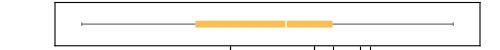

```mathematica
With[{data=noise[[2;;,2]]},
{q1,median,q3}=N[Quartiles[data]];
iqr=q3-q1;
bw2=BoxWhiskerChart[data,{"Outliers",{"Outliers","●"},{"FarOutliers","○"}},AspectRatio->1/10,ImageSize->500,BarOrigin->Left,GridLines->{{{q3+1.5iqr,Dashed},{q3+3iqr,Dashed}},None},
FrameTicks->{{None,None},{data,{{q1,"q1"},{q3,"q3"},{q3+1.5iqr,"near"},{q3+3iqr,"far"}}}}]]
```

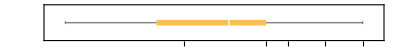

```mathematica
Show[bw2,FrameLabel->{{None,None},{RawBoxes[RowBox[{"Valor"," ","de"," ",RowBox[{"precisión","."}]}]],None}},PlotLabel->HoldForm[Distribución por cuartil. (Ruido de Pauli)],LabelStyle->{13,GrayLevel[0]}, ImageSize->Full]
```

```mathematica
Export[ "distribution_q_ansatz_noise_credit.pdf",%]
```

distribution_q_ansatz_noise_credit.pdf

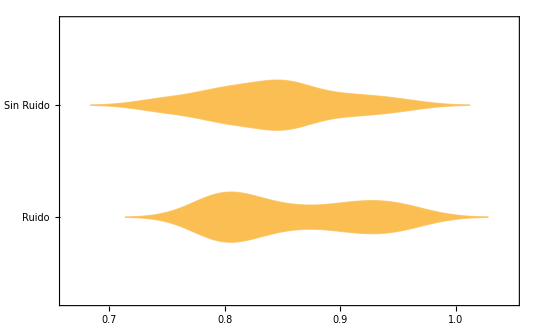

```mathematica
DistributionChart[{x,y},BarOrigin->Right,ChartLabels->{"Ruido","Sin Ruido"},ScalingFunctions->"Reverse"]
```